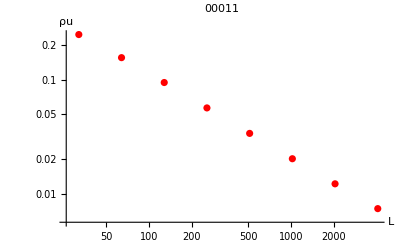

Import::hdrs: The value 1 for the option "HeaderLines" is outside of the data range.

Part::partw: Part {1,2} of {} does not exist.

Part::partw: Part 2 of {{}} does not exist.

Part::partd: Part specification All⟦1⟧ is longer than depth of object.

Part::partd: Part specification All⟦2⟧ is longer than depth of object.

Part::pkspec1: The expression {All⟦1⟧,All⟦2⟧} cannot be used as a part specification.

Part::pkspec1: The expression True cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLogLogPlot::lpn: {{},{{}}⟦2⟧}⟦{All⟦1⟧,All⟦2⟧},{1,2}⟧ is not a list of numbers or pairs of numbers.

ListLogLogPlot[{{},{{}}⟦2⟧}⟦{All⟦1⟧,All⟦2⟧},{1,2}⟧,PlotLabel→01011,AxesLabel→{L,ρu},PlotStyle→RGBColor[1, 0, 0]]

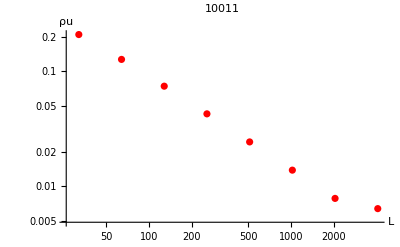

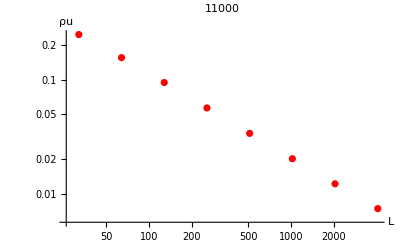

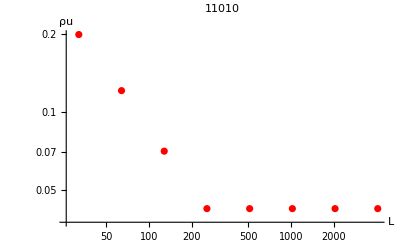

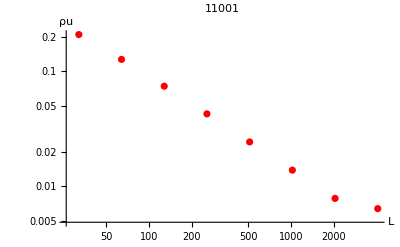

```mathematica
rules = {"00011","01011","10011","11000","11010","11001"};
data = {};
Do[AppendTo[data ,Import["/home/vynie/Documents/PycharmProjects/gameoflife (cópia)/Output/ScriptOutput/"<>rules[[i]]<>"/rand/L_x_Insats.csv",HeaderLines->1]];
data[[i]] = data[[i]][[All, {1, 2}]];
data[[i]]= Map[{#[[1]],#[[2]]}&,data[[i]]];
logData=Map[{#[[1]],#[[2]]}&,data[[i]]];
graph1 = ListLogLogPlot[logData, PlotLabel->rules[[i]], AxesLabel->{"L", "ρu"}, PlotStyle->Red];
Print[graph1],
(*graph1 = ListLogLogPlot[data[[i]], PlotLabel->rules[[i]], AxesLabel->{"L", "ρu"}, PlotStyle->Red];
logData=Map[{N[Log[#[[1]]]],Log[#[[2]]]}&,data[[i]]];
f[x_]:=Evaluate[Fit[logData, {1, x}, x]];
graph2 = Plot[f[x],{x, -100, 5000}, PlotStyle->{Dashed,Black}];
Print[Show[graph1, graph2]];
Print[f[x]],*)


{i, 1,Length[rules]}]
```